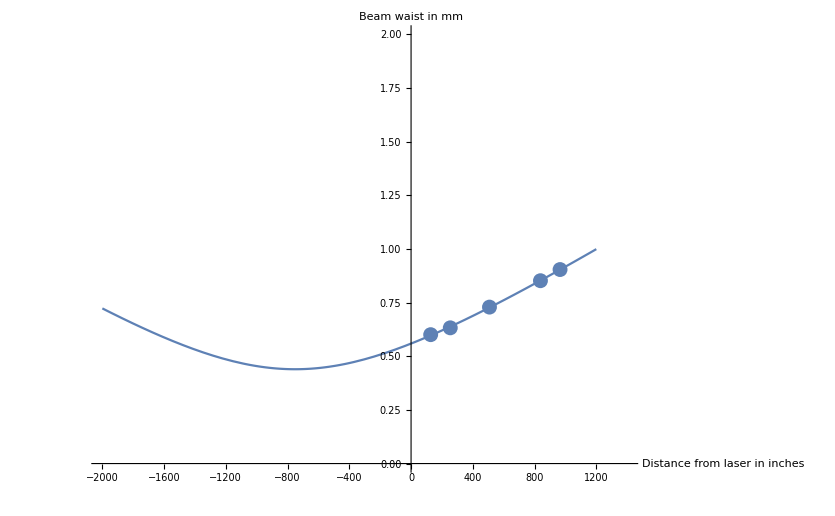

The location of the initial beam waist is -751.464 mm, and it has a radius of 0.439583 mm.

```mathematica
Remove["Global`*"];

allzdata={{5,.600655},{10,.632534},(*{15,.99773},*){20,.729086},{33,.852107},{38,.904124}(*,{43,1.23857},{48,1.26888}*)};
allzdata=allzdata/.{z_,w_}->{25.4*z,w};
λ=635*10^-6;
zr=(π w0^2)/λ;
CurveFit[z_]=FindFit[allzdata,{w0 √(1+(z-z0)^2/zr^2)},{z0,w0},z];
w0=w0/.CurveFit[z][[2]];
z0=z0/.CurveFit[z][[1]];
Show[{Plot[w0 √(1+(z-z0)^2/zr^2),{z,-2000,1200},
PlotRange->{{-2000,1400},{0,2}},AxesLabel->{"Distance from laser in inches","Beam waist in mm"}],
ListPlot[allzdata]}]
Print["The location of the initial beam waist is " ,z0," mm, and it has a radius of ",w0," mm."]
```

```mathematica
|
```

```mathematica
Remove["Global`*"];
Element[{s1,s2,f1,f2},Reals];

λ=635*10^-6;
zr=(π w0^2)/λ;
n=1;
qi[z_]=(z-z0)+ⅈ zr;
w[z_]=w0 √(1+(z-z0)^2/zr^2);

space1=({{1, s1}, {0, 1}});
lens1=({{1, 0}, {-1/f1, 1}});
space2=({{1, s2}, {0, 1}});
lens2=({{1, 0}, {-1/f2, 1}});

as1=space1[[1]][[1]];
bs1=space1[[1]][[2]];
cs1=space1[[2]][[1]];
ds1=space1[[2]][[2]];
qs1[z_]=(as1 qi[z]+bs1)/(cs1 qi[z]+ds1);

al1=lens1[[1]][[1]];
bl1=lens1[[1]][[2]];
cl1=lens1[[2]][[1]];
dl1=lens1[[2]][[2]];
ql1[z_]=(al1 qs1[z]+bl1)/(cl1 qs1[z]+dl1);

as2=space2[[1]][[1]];
bs2=space2[[1]][[2]];
cs2=space2[[2]][[1]];
ds2=space2[[2]][[2]];
qs2[z_]=(as2 ql1[z]+bs2)/(cs2 ql1[z]+ds2);

al2=lens2[[1]][[1]];
bl2=lens2[[1]][[2]];
cl2=lens2[[2]][[1]];
dl2=lens2[[2]][[2]];
ql2[z_]=(al2 qs2[z]+bl2)/(cl2 qs2[z]+dl2);


(*qf[z_]=(z-zf0)+ⅈ zfr*)
z0=-751.464;
w0=.439583;

zminuszf0[z_,s1_,s2_,f1_,f2_]=ComplexExpand[Re[ql2[z]]];
wf0[z_,s1_,s2_,f1_,f2_]=√((λ ComplexExpand[Im[ql2[z]]])/π)//Simplify;
NewWaistWidth[s1_,s2_,f1_,f2_]=wf0[0,s1,s2,f1,f2];

zf0[z_]=zf0/.Solve[zminuszf0[z,s1,s2,f1,f2]==z-zf0,zf0][[1]]//Simplify;
NewWaistLocation[s1_,s2_,f1_,f2_]=zf0[0]+s1+s2;
Manipulate[
Show[{
Plot[NewWaistWidth[s1,s2,f1,f2] √(1+(z-NewWaistLocation[s1,s2,f1,f2])^2/(((π NewWaistWidth[s1,s2,f1,f2]^2)/λ)^2)),{z,0,3500},PlotRange->{{0,3500},{-2,2}}],
Plot[-NewWaistWidth[s1,s2,f1,f2] √(1+(z-NewWaistLocation[s1,s2,f1,f2])^2/(((π NewWaistWidth[s1,s2,f1,f2]^2)/λ)^2)),{z,0,3500}],
Graphics[{Text[NewWaistWidth[s1,s2,f1,f2],{1000,1.5}],Text[NewWaistLocation[s1,s2,f1,f2],{1000,1}]}]

}],
{s1,0,500},{s2,0,500},{f1,100,1000},{f2,100,1000}]
```

```mathematica
membrane=500;
detector=3500;
setoflenses={-50,-75,-100,500,750,1000};
setofcombinations=Tuples[setoflenses,{2}];
waistmembrane[s1_,s2_,f1_,f2_]=NewWaistWidth[s1,s2,f1,f2] √(1+(membrane-NewWaistLocation[s1,s2,f1,f2])^2/(((π NewWaistWidth[s1,s2,f1,f2]^2)/λ)^2));
waistdetector[s1_,s2_,f1_,f2_]=NewWaistWidth[s1,s2,f1,f2] √(1+(detector-NewWaistLocation[s1,s2,f1,f2])^2/(((π NewWaistWidth[s1,s2,f1,f2]^2)/λ)^2));
MemSet[s1_,s2_]=Table[waistmembrane[s1,s2,setofcombinations[[i]][[1]],setofcombinations[[i]][[2]]],
{i,1,Length[setofcombinations]}];
DetSet[s1_,s2_]=Table[waistdetector[s1,s2,setofcombinations[[i]][[1]],setofcombinations[[i]][[2]]],
{i,1,Length[setofcombinations]}];
Length[setofcombinations];
nameset=Table[ToString[setofcombinations[[i]]],{i,1,Length[setofcombinations]}];
Manipulate[
PairedBarChart[MemSet[s1,s2],DetSet[s1,s2],ChartLabels->nameset,PlotRange->{0,10},ChartStyle->{{Red,Blue},None,None},ChartLegends->{{"Membrane Spot Size mm", "Detector Spot Size mm"}, None, None}],{s1,0,500},{s2,0,500}]
```